```mathematica
(*Definimos parametros y constantes*)
a=1/10;
b=4;
c=4;
h=1;
w=1;
```

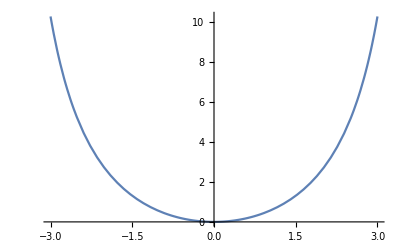

```mathematica
(*Masa varibale y potencial*)
m=b*c/((b+x)*(c-x));
V = (m*w^2*x^2)/2;
Plot[V,{x,-3,3}]
```

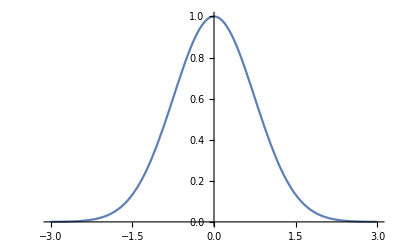

```mathematica
f[x_,a_]:=Exp[-x^2*(1-a)]
Plot[f[x,a],{x,-3,3}]
```

```mathematica
phi0=Cos[(1/2)*t/h];
phi1=Cos[-(3/2)*t/h];
phi2=Cos[-(5/2)*t/h];
phi3=Cos[-(7/2)*t/h];
phi4=Cos[-(9/2)*t/h];
phi5=Cos[-(11/2)*t/h];
(*phi0=Exp[-I*1/2*t];
phi1=Exp[-I*3/2*t];
phi2=Exp[-I*5/2*t];
phi3=Exp[-I*7/2*t];
phi4=Exp[-I*9/2*t];
phi5=Exp[-I*11/2*t];*)
```

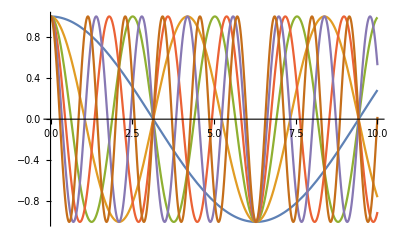

```mathematica
Plot[{phi0,phi1,phi2,phi3,phi4,phi5},{t,0,10}]
```

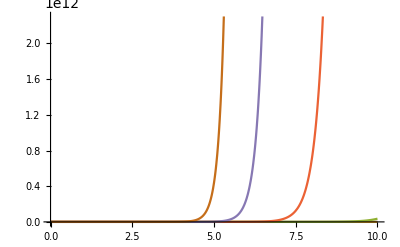

-Graphics-

```mathematica
g=Integrate[x*m/f[x,a],x];
c = 1/Sqrt[Integrate[(Exp[-(w/h)*g])^2,{x,-c,b}]];
Psi0=Exp[-(w/h )*g];
Psi1=(1/Sqrt[1!])*(m*w*x*Psi0-h*f[x,a]*D[Psi0,x])/Sqrt[2*m*h*w];
Psi2=(1/Sqrt[2!])*(m*w*x*Psi1-h*f[x,a]*D[Psi1,x])/Sqrt[2*m*h*w];
Psi3=(1/Sqrt[3!])*(m*w*x*Psi2-h*f[x,a]*D[Psi2,x])/Sqrt[2*m*h*w];
Psi4=(1/Sqrt[4!])*(m*w*x*Psi3-h*f[x,a]*D[Psi3,x])/Sqrt[2*m*h*w];
Psi5=(1/Sqrt[5!])*(m*w*x*Psi4-h*f[x,a]*D[Psi4,x])/Sqrt[2*m*h*w];
```

Sum::vloc: The variable Psi1 phi1 cannot be localized so that it can be assigned to numerical values.

∑_(Psi1 phi1) ∑_(Psi2 phi2) ∑_(Psi3 phi3) ∑_(Psi4 phi4) ∑_(Psi5 phi5) Psi0 phi0

General::munfl: Exp[-3663.91] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NSum::write: Tag Times in Psi1 phi1 is Protected.

General::stop: Further output of NSum::write will be suppressed during this calculation.

NSum::nliter: Non-list iterator Psi1 phi1 at position 2 does not evaluate to a real numeric value.

General::stop: Further output of NSum::nliter will be suppressed during this calculation.

-Graphics-

```mathematica
Plot3D[Psi2*phi2,{x,-3,3},{t,0,25},PlotLegends->{"ψ_0","ψ_1","ψ_2","ψ_3","ψ_4","ψ_5","V(x)"},PlotLabel->"Funciones de onda",AxesLabel->{"x","t","ψ(x)"},PlotRange->All]
```

General::munfl: Exp[-3657.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics3D-